# From Riemann Zeta Function to Riemann Hypothesis

The Riemann Hypothesis is the conjecture that all non-trivial zeros of the Riemann Zeta function ζ(s) lie on the critical line Re(s)=1/2 .

Lanston Hau Man Chu, Jun. 28,  2018

The Riemann hypothesis is an important unsolved problem raised by Bernhard Riemann in 1859. It is one of the seven Millennium Prize Problems and many other mathematics propositions would be proven to be true under the Riemann hypothesis. The problem plays an important role in analytic number theory and has a wide scope of applications in physics, probability theory, and applied statistics. In the past 160 years since the conjecture came into being, lots of progress has been made by brilliant mathematicians, yet it still remains unsolved. The proof of this hypothesis will be a great triumph in mathematics. This essay will begin with Riemann Zeta function ζ(s) and goes on to illustrate relevant concepts of the Riemann hypothesis.

The handwritten script of Riemann’s 1859 paper, “On the Number of Primes Less Than a Given Magnitude”:

```mathematica
Image[Import["https://c1.staticflickr.com/3/2600/3741306561_3c358277b7_b.jpg"],Magnification->0.3]
```

-Graphics-

## Initialization Cell

The below codes are for initialization:

```mathematica
ClearAll["Global`*"]

conformalMapGraphic[f_, L_, pp_, adjX_, adjY_] :=
  Module[{netℂ, net},
   gX = <|0 -> {-L, L}, 1 -> {1.01, L}, -1 -> {-L, 1.01}|>;
   gY = <|0 -> {-L, L, ControlActive[8 L/pp, 4 L/pp]}, 1 -> {2, 3, 2}|>;
   adjX1 = gX[adjX][[1]]; adjX2 = gX[adjX][[2]];
   adjY1 = gY[adjY][[1]]; adjY2 = gY[adjY][[2]]; adjY3 = gY[adjY][[3]];
   netℂ = Table[Evaluate[N[f[x + I y]]], {x, adjX1, adjX2, ControlActive[8 L/pp, 4 L/pp]}, {y, adjY1, adjY2, adjY3}];
   net = MapThread[List, {Re[netℂ], Im[netℂ]}, 2];
   Quiet[Graphics[{MapIndexed[{Blue, Line[#]} &, net],
      MapIndexed[{Purple, Line[#]} &, Transpose[net]]}]]];

plot0[title_]:=ListPlot[{},];
```

## Riemann Zeta Function

The Riemann zeta function ζ (s) is a complex function which gives the sum of the Dirichlet series.

The formula of ζ (s):

```mathematica
HoldForm[ζ[s]=Sum[Power[n^s,-1],{n,1,∞}]=Power[1^s,-1]+Power[2^s,-1]+"..."]
```

ζ[s]=∑_(n=1)^∞ 1/n^s=1/1^s+1/2^s+...

For example, the famous ζ (2) was first found by Euler in 1735 (Derbyshire 2004, p .64) or 1736 (Srivastava 2000).

Value of ζ (2):

```mathematica
HoldForm[ζ[2] = Power[1^2, -1] + Power[2^2, -1] + "..." = Divide[Power[Pi,2],6]]
```

ζ[2]=1/1^2+1/2^2+...=π^2/6

## Components of the Summation

For input on the complex plane (e.g. ζ (2 +y I)), in each component 1/n^(2+y ⅈ), we can separate it into  1/n^2 1/n^(y ⅈ) to understand the function’s behavior. As we know, The former is real (i.e. the magnitude), while the latter is a rotation as 1/n^(y ⅈ)=ⅇ^(-y ⅈ Log(n))(i.e. the argument).

ⅇ^(-y I) (i.e. yellow spot) is changed with y (i.e. blue spot) as below :

```mathematica
Animate[Show[ListPlot[{{{0,y}},{ReIm@(ⅇ^(-y ⅈ))}},],Graphics@Circle[{0,0},1],],{y,0,1.5,},]
```

The magnitude  1/n^2would reduce when n increases, and thus 1/n^(2+y ⅈ) would reduce and rotate anti-clock-wisely. Therefore the sum of the above (i.e. ζ(s)) should give us a spiral path.

Values of 1/n^(2+y ⅈ) and  ∑_(n=1)^∞ 1/n^(2+y ⅈ), while ζ(2 + y ⅈ) is indicated by a  red spot:

```mathematica
ptsSepar[y_]=(Thread[{a,ReIm@Table[1/n^(2+y ⅈ),{n,1,100}]}]/.a->{0,0}) ;
pRed[z_,n_]:=ListPlot[{ReIm@(zValue=z^(1-n) Zeta[z]^n)}->{Round[zValue,0.01]},];
Manipulate[GraphicsRow[{ListLinePlot[ptsSepar[y],],Show[ListLinePlot[Partition[FoldList[#1+#2&,{0,0},ptsSepar[y][[All,2]]],2,1],],pRed[2+y ⅈ,1]]},],{{y,2},1,5,},SaveDefinitions->True]
```

## Extension of Domain

Now, we would extend our domain from a specific point to horizontal lines. For the horizontal line s = x + 2 I (denoted by 𝕃), when x > 1, ζ(s) can be well defined (otherwise the magnitude of 1/n^xwould be divergent). The right part of the line (denoted by 𝕃’) would be mapped to an arc sitting in the 4^th quadrant.

The transformation of ζ(𝕃’), where 𝕃’ is the line  x + 2 I, where x > 1. The red spot is referring to 2 + 2 ⅈ ↦ ζ(2 + 2 ⅈ):

```mathematica
Manipulate[Show[plot0["Mapping s↦ζ(s) on the line x + 2 I, where x > 1"],conformalMapGraphic[#^(1-n)Zeta[#]^n&,8,500,1,1],pRed[2+2 ⅈ,n],],{n,0,1},SaveDefinitions->True]
```

In fact, ζ(s) can be well defined on the entire half plane Re(s) > 1 (denoted by ℂ’). We now extend the domain from 𝕃’ to ℂ’, and ζ(ℂ’) are within the 1^st and 4^th quadrant.

Given the regular grid 𝔾 in ℂ’, where ℂ’ is the right part of complex plane where Re(s)>1. The transformation ζ (𝔾):

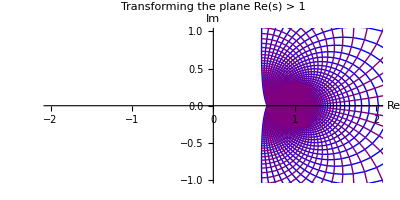

```mathematica
{zp1,zp2}=Table[conformalMapGraphic[Zeta@#&,8,500,adjX,0],{adjX,{0,1}}];
Show[plot0["Transforming the plane Re(s) > 1"],zp2,]
```

We can see that we have map ℂ’ to ℂ’’, where ℂ’’ is the plane where Re(s)>1/2. But we want to map the entire ℂ instead of ℂ’ as the domain. To do this, we need analytic continuation. Below we would introduce the concept of the conformal map.

## Conformal Map and Analytic Functions

We consider the mapping z ↦ z^2, which maps 2+2 I to 8:

Animation of z ↦ z^2, at 2 + 2 ⅈ ↦8 :

```mathematica
pts1={{2,2}}; zsqrt[n_,{x_,y_}]=ReIm@((x+y ⅈ)^n);
p1a[n_,pts_,pr_,ps_,title_]:=ListPlot[zsqrt[n,#]&/@pts,];
Animate[p1a[n,pts1,{{0,4},{0,8}},0.03,"Mapping 2 + 2 ⅈ ↦8"],{n,1,2,},]
```

We can even transform the entire ℂ.

Transformation of z ↦ z^2 for the regular grid in ℂ:

```mathematica
Animate[Show[plot0["Mapping z ↦ z^2"],conformalMapGraphic[#^n&,1, 64,0,0],],{{n,1,"n"},1,2,},]
```

We can see that every right angle (except those at the origin) are preserved under the transformation z ↦ z^2. In fact, if every angle in the set Ω are preserved. Mappings with this property are called Conformal Map on Ω, or analytic function on Ω.

Demonstration of the preservation of an angle of 18.43 ° during the mapping z↦z^2:

```mathematica
yD1=Range[.5,2,.01];xD1=Range[.25,1,.005];xD2=Range[.25,1.75,.01];
pts2=Join[Thread[{yD1,xD1}],Thread[{yD1,xD2}]];
Animate[Legended[p1a[n,pts2,{{0,2},{0,2}},0.01,"Mapping z↦z: Preservation of Angle"],Placed[Style["18.43°↑"],{.1,.05}]],{n,1,2,},]
```

We can have some other conformal maps. For example, z ↦ ⅇ^z.

Transformation of z ↦ ⅇ^z for the regular grid in ℂ:

```mathematica
Animate[Show[plot0["Mapping z ↦ ⅇ^z"],conformalMapGraphic[#^(1-n) ⅇ^(# n)&,1, 64,0,0],],{{n,0,"n"},0,1,},]
```

And z ↦ sin(z π).

Transformation of z ↦ sin(z π) for the regular grid in ℂ:

```mathematica
Animate[Show[plot0["Mapping z ↦ sin(z π)"],conformalMapGraphic[#^(1-n) Sin[# π]^n&,1, 64,0,0],],{{n,0,"n"},0,1,},]
```

## Analytic Continuation of Riemann Zeta Function

Let f_1 and f_2 be analytic functions on domains Ω_1 and Ω_2, respectively, and suppose that the intersection  Ω_1∩Ω_2 is not empty and that f_1=f_2 on Ω_1∩Ω_2 . Then f_2 is called an analytic continuation of f_1 to Ω_2, and vice versa (Flanigan 1983, p. 234).

The uniqueness theorem is an extremely powerful statement, which states that by knowing the value of a complex function in some finite complex domain, it would uniquely determine the value of the function at every other point. By the uniqueness theorem, we can uniquely determine an analytic function for ζ(s), which extend the domain from ℂ' to ℂ.

Analytic continuation for the entire ζ(ℂ):

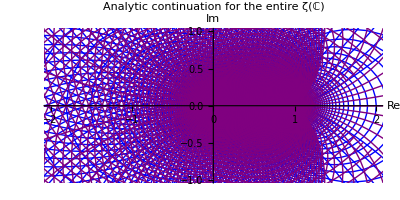

```mathematica
Show[plot0["Analytic continuation for the entire ζ(ℂ)"],zp1,]
```

By extending the Re(z) > 1 to Re(z) ∈ ℝ, we cover the entire ℂ as domain. now we even cover the input of -1, resulting the famous Ramanujan summation, which have applications on String Theory:-

The Ramanujan summation:

```mathematica
HoldForm[ζ[-1]=1+2+3+"..." = Divide[-1,12]]
```

ζ[-1]=1+2+3+...=-1/12

In 1913, G. H. Hardy received a letter from Srinivasa Ramanujan. There were 11 pages of mathematical formulae, including that the sum of all positive integers can be thought of being equal to -1/12.

The image of Ramanujan' s original letter :

```mathematica
Import["http://blog.stephenwolfram.com/data/uploads/2016/04/surprising-claims-from-ramanujan-letter-to-hardy.png"]
```

-Graphics-

## Riemann Hypothesis

We are interested in the zeros of the Riemann Zeta function, i.e. the s such that ζ (s) = 0. It can be easily proved that all negative even number are zeros of ζ(s). That is,

The map s ↦ ζ (s) from s = -1 to -6. The negative even numbers are the trivial zeros.

```mathematica
Column@Thread[(rg=Range[-6,-1,1])->(Zeta[#]&/@rg)]
```

-6→0
-5→-1/252
-4→0
-3→1/120
-2→0
-1→-1/12

Dating back to 1859, Bernhard Riemann proved that all non-trivial zeros of ζ(s) lie in the region 0 ≤Re(s)≤1 (i.e. the critical strip).  He further conjectured that all these zeros lie on the line Re(s)=1/2 (i.e. the critical line).

The region of zeros of Riemann Zeta Function:

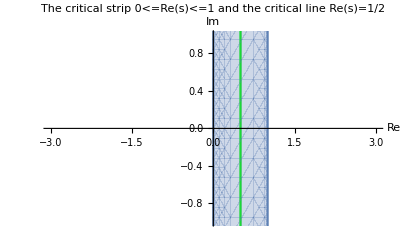

```mathematica
pLine=ListLinePlot[{{.5,-40},{.5,40}},];
Show[pLine,RegionPlot[0≤x≤1,{x,-2,2},{y,-2,2}],]
```

In 1896, Hadamard and Vallée-Poussin have proved independency that the non-trivial zeros lie in the region  0 <Re(s)<1, but we still have a far way to go. As we can see, when s moves along the line Re(s)=1/2, ζ(s) passes through the origin again and again:-

Demonstration on how ζ(s) passes through the origin when s is at the zeros (denoted in red):

```mathematica
h[{x_,y_}]=ReIm@Zeta[x+y ⅈ];
pz1a[pts_]:=ListPlot[h[#]&/@pts,];
p2=ListPlot[ReIm@(ZetaZero/@Complement[Range[-6,6],{0}]),];
p3[y_]:=ListPlot[{{0.5,y}},];

Animate[GraphicsRow[{pz1a[{.5,#}&/@Range[-40,y,0.1]],Show[pLine,p2,p3[y],]}, ],{y,-40,40,},]
```

At the time of writing, it is known that all zeros of ζ(s) lie between the region 0< Re(s) <1. We have not yet found any non-trivial zeros outside the line  Re(s)=1/2, but we don’t have a proof that they really don't exist. The statement that all zeros lie at the line Re(s)=1/2 is called the Riemann hypothesis.

Last but not least, below is a the Riemann zeta function ζ(z) plotted with domain coloring, for the benefit of the readers.

Domain coloring of ζ(s):

```mathematica
Quiet@Graphics@RasterArray[Table[Hue@((Arg@Zeta[σ+I t])/(2 π)),{t,-20,20,.1},{σ,-10,10,.1}]]
```

-Graphics-

## Further explorations

Analytic continuation
Conformal Map

## References

Derbyshire, J.Prime Obsession : Bernhard Riemann and the Greatest Unsolved Problem in Mathematics.New York : Penguin, 2004.

Flanigan, F. J. Complex Variables : Harmonic and Analytic Functions. New York : Dover, 1983.

Krantz, S. G. “Uniqueness of Analytic Continuation” and “Analytic Continuation.” §3 .2 .3 and Ch. 10 in Handbook of Complex Variables. Boston, MA : Birkhäuser, pp. 38 - 39 and 123 - 141, 1999.

Srivastava, H. M. “Some Simple Algorithms for the Evaluations and Representations of the Riemann Zeta Function at Positive Integer Arguments.” J. Math. Anal. Appl. 246, 331 - 351, 2000.

## Author contact information

Lanston Hau Man Chu
06.28.2018
Email: lanstonchu@gmail.com
Blog: https://lanstonchu.wordpress.com/